```mathematica
link=Install[LinkConnect["43951@192.168.150.128,46839@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-100,Ωhe=1/4,θrp=0.45,θrhe=0.225,θe=Sqrt[0.8],θb=0.045,ωb=14.2302,ωe=150,
ωpp ={0.0282,0.1017,0.2466,0.4228,0.5766,0.6963,0.7895,0.8619,0.9164,0.9546,0.9772,0.9847,0.9772,0.9546,0.9164,0.8619,0.7895,0.6963,0.5766,0.4228,0.2466,0.1017,0.0282},
ωphe={0.00016,0.0096,0.0876,0.2064,0.2893,0.3498,0.3966,0.4329,0.4603,0.4795,0.4909,0.4947,0.4909,0.4795,0.4603,0.4329,0.3966,0.3498,0.2893,0.2064,0.0876,0.0096,0.00016},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωpp,θrp,θrp,vd,vr]],
Thread[wstpDRingDistribution[Ωhe,ωphe,θrhe,θrhe,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
sol=With[{k=1.1,wna=89Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.501,-0.006] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

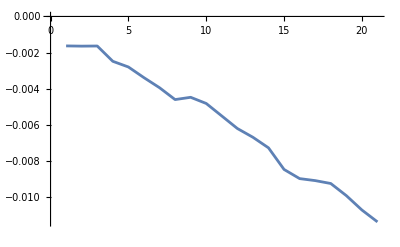

```mathematica
sol=With[{k=Range[0.5,1.5,0.05],wna=89Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.498,-0.0016] (1+0.0001 I {0,1,2}),MaxIterations->100]];
ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[21]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["0.5.txt",gama];
```

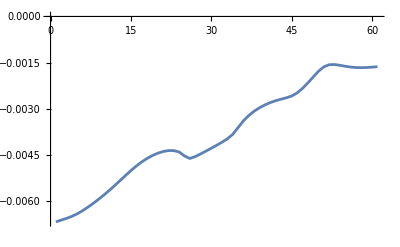

```mathematica
check=With[{k=Range[1.1,0.5,-0.01],wna=89Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.5012,-0.0066] (1+0.0001 I {0,1,2}),MaxIterations->100]];
ListLinePlot[Im[check[[2,2]]]]
```